# MATH7501 Practical 9 (Week 10), Semester 1-2021

## Topic: Sequences & Series, Limits and Derivatives

Author:  Aminath Shausan
Date: 7-05-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 5 to 8 contents  of the reading materials for MATH7501

# Resources

Chapters 5 to 8 of course reader

# Q1 Limit

Calculate limit_(x → Infinity) sin(e^-x) and explain why this is true

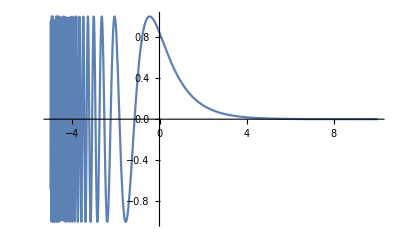

```mathematica
Plot[Sin[Exp[-x]], {x, -5, 10}]
```

```mathematica
limit e^{-x} is 0 as x approaches Infinity. sin(0) is continuous. Then sin(e^-x) = 0 as x approaches Infinity.
```

# Q2 Limit

Calculate limit_(x → Infinity) 1/(cos(x) +x)

```mathematica
-1 +x≤ cos(x)+x ≤ 1+x
For x> 1 , 1/(1 +x)≤ 1/(cos(x)+x)≤ 1/(x-1)
As Subscript[limit, x-> Infinity] 1/(-1 +x) =0   and Subscript[limit, x-> Infinity] 1/(1 +x) =0  , then by the sqeez theorem  Subscript[limit, x -> Infinity] 1/(cos(x) +x) =0
```

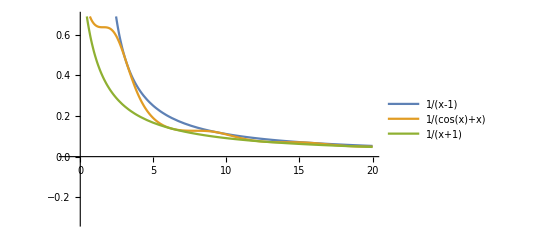

```mathematica
Plot[{1/(x-1),1/(Cos[x]+x),1/(x+1)},{x,-1,20}, PlotLegends->"Expressions"]
```

# Q3 Continuous function

Consider the function 
f(x) = {(sin(x))/x          , x>0
1       ,x≤0          
 Show that this function is continuous for all x.

```mathematica
Hint: Continuous at a point (see Section 6.4, Definition 12)
              Continuous on interval (see pg 104)
f(x) is continuous everywhere except possibly x=0. So check continuity at x=0.
Check: (1) Is f(0) defined? yes f(0) =1
          (2) Does Subscript[limit, x-> 0] f(0) exist? 
     (3) Is Subscript[limit, x-> 0] f(x) = f(0)
Subscript[limit, x-> SuperMinus[0]] f(x) = f(0) =1
Subscript[limit, x-> SuperPlus[0]] f(x) = sin(x)/x =1 
Thus condition (3) is satisfied .Thus f(x) is continuous for all x.
```

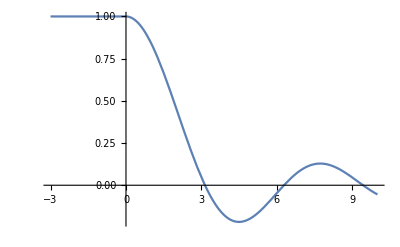

```mathematica
Plot[Piecewise[{{1,x≤0},{Sin[x]/x,x>0}}],{x,-3,10}]
```

# Q4 IVT and MVT

a) Consider the function f(x)=x^4+x+1. Show that this function does not cross the x-axis.

```mathematica
let y=f(x)
Find x value at f'(x)=0 (this gives any critical points)
Substitute the value of x in f(x) to get the value of y
```

```mathematica
step1: solve for x in  f'(x)=0 (you should get just one critical point)
step 2:find f''(x) and show that  the critical point is global minimum (f''(x) >0)
```

b)Consider the new function f(x)=x^4+x-1. Show that there are exactly two solutions to f(x)=0,using Intermediate Value Theorem (IVT)and Mean Value Theorem (MVT).

```mathematica
IVT (look at pg 105)
MVT (look at pg 115)
```

# Q5 Series

Determine if the following sums converge or not. If they do,work out their limit
a) ∑_(n=1)^∞ n^(2/e)

(b)∑_(n=0)^∞ (π -e)^n